```mathematica
o = {0,0,0}
```

{0,0,0}

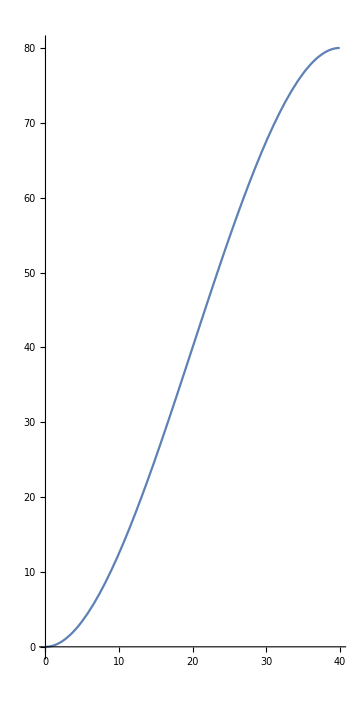

```mathematica
ParametricPlot[{5t,3/400*((-(5t)^3)/3+20*(5t)^2)},{t,0,8},ImageSize->Medium]
```

```mathematica
Solve[3/400*((40)^3/-3+20*(40)^2)==40*Tan[t],t,Reals]
```

{{t→ConditionalExpression[-2 ArcTan[1/2 (1+√5)]+2 π C[1],C[1]∈ℤ]},{t→ConditionalExpression[2 (ArcTan[1/2 (-1+√5)]+π C[1]),C[1]∈ℤ]}}

```mathematica
(40)^2/-3+20*(40)
```

800/3

```mathematica
ArcTan[800/3]//Simplify
```

ArcTan[800/3]

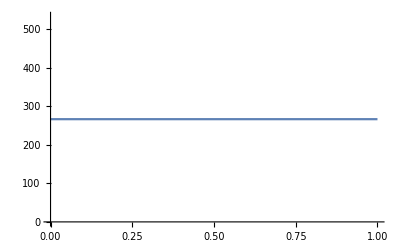

```mathematica
Plot[800/3,{x,0,1}]
```

```mathematica
Plot3D[Sqrt[x+y+1]/(x-1),{x,-10,10},{y,-10,10},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Solve[{78*a+39*b+c==508,40*a+76*b+2*c==430,3*b+108*c==117},{a,b,c}]
```

{{a→5,b→3,c→1}}

```mathematica
Solve[5.55*4186*(92.5-x)==3.30*33.5*10^4+3.30*4186*(x),x]
```

{{x→28.1673}}

```mathematica
28.167+273
```

301.167

```mathematica
3.30*33.5*10^4/273
```

4049.45

```mathematica
3.30*4186*Log[E,301.167/273]
```

1356.42

```mathematica
5.55*4186*Log[E,301.167/(92.5+273)]
```

-4497.8

```mathematica
NIntegrate[Integrate[1-x^2-y^2,{y,-Sqrt[1-x^2],Sqrt[1+x^2]}],{x,-1,1}]
```

1.19537

```mathematica
Integrate[Sqrt[E^(-2 r^2)*4*r^2+1],{dr,0,4}]
```

4 √(1+4 ⅇ^(-2 r^2) r^2)

```mathematica
f[r_]=4 √(1+4 ⅇ^(-2 r^2) r^2);
```

```mathematica
f[4]-f[0]
```

-4+4 √(1+64/ⅇ^32)

```mathematica
NIntegrate[-4+4 √(1+64/ⅇ^32),{dx, 0, 2*Pi}]
```

1.01846×10^-11

```mathematica
NIntegrate[Integrate[Sqrt[64 x^2+32x+14],{x,1,4}],{y,0,1}]
```

66.7579

```mathematica
Show[ContourPlot3D[{z+y==1},{y,-3,3},{z,-3,3},{x,-3,3},AxesLabel->Automatic],
ContourPlot3D[{y==x^2,z==0},{y,-3,3},{z,-3,3},{x,-3,3}]]
```

-Graphics3D-